# Buildings and Roads Data Extraction

## Generation Routines

## Choose Place

```mathematica
placeID="Catemaco";
{filteringPoints,manualPoints}={500,500};
```

## Functions and Libraries

### Main

```mathematica
{placeName,filterRatio}={placeID,20};
{imageSize,imageResolution}={2500,200};
(**)
SetDirectory[NotebookDirectory[]];
shapeFilesPaths={"./SHP/Buildings/","./SHP/Roads/"};
buildingPath=shapeFilesPaths[[1]]<>placeName<>"/"<>placeName<>".shp";
roadPath=shapeFilesPaths[[2]]<>placeName<>"/edges/"<>"edges"<>".shp";
```

### Other

```mathematica
<<PajaroLocoPublic`
ListPlotPoints[points_]:=ListPlot[points,
Frame->True,
Axes->True,
FrameStyle->Thickness[.005],
ImageSize->800,
FrameTicksStyle->None,
PlotStyle->PointSize[.025],
AspectRatio->1
]Options[EdgesStyleList2]:={LineThickness->.004,VariableStyle->"Both"}
EdgesStyleList2[vertexSyllableList_,OptionsPattern[]]:=Switch[OptionValue[VariableStyle],"LineColor",Table[DirectedEdge[vertexSyllableList[[i]][[1]][[1]],vertexSyllableList[[i]][[1]][[2]]]->{ColorData[{"LakeColors","Reverse"}][vertexSyllableList[[i]][[2]]],Thickness[OptionValue[LineThickness]]},{i,1,Length[vertexSyllableList]}],"LineWidth",Table[DirectedEdge[vertexSyllableList[[i]][[1]][[1]],vertexSyllableList[[i]][[1]][[2]]]->{Black,Thickness[vertexSyllableList[[i]][[2]]*OptionValue[LineThickness]]},{i,1,Length[vertexSyllableList]}],"Both",Table[DirectedEdge[vertexSyllableList[[i]][[1]][[1]],vertexSyllableList[[i]][[1]][[2]]]->{ColorData[{"LakeColors","Reverse"}][vertexSyllableList[[i]][[2]]],Thickness[vertexSyllableList[[i]][[2]]*OptionValue[LineThickness]]},{i,1,Length[vertexSyllableList]}],_,Table[DirectedEdge[vertexSyllableList[[i]][[1]][[1]],vertexSyllableList[[i]][[1]][[2]]]->{Thickness[OptionValue[LineThickness]]},{i,1,Length[vertexSyllableList]}]]
edgeshape[e_,___]:={Arrowheads[{{.0001,.5}}],Arrow[e]}
Options[GraphTransitionsFrequenciesWithMax]:={ImagePadding->None,Background->White,VertexStyle->Automatic,VertexCoordinates->Automatic,LineThickness->.0005,VariableStyle->"Both",GraphLayout->Automatic,Frame->True,FrameStyle->Thick,ImageSize->Automatic,VertexSize->.5,EdgeShapeFunction->edgeshape,VertexLabelStyle->{Italic},Prolog->{},Epilog->{},VertexShape->Automatic}
GraphTransitionsFrequenciesWithMax[frequenciesOutput_,max_,OptionsPattern[]]:=Module[{frequencies,syllables,edges,fixedEdgesList,vertexSyllableList,normalizedVertexSyllableList,edgesStyleList,links},frequencies=frequenciesOutput[[1]];
syllables=frequenciesOutput[[2]];
edges=Table[DirectedEdge[i,j]->frequencies[[i,j]],{i,Length[syllables]},{j,Length[syllables]}]//Flatten;
fixedEdgesList=DeleteCases[edges,DirectedEdge[_,_]->0];
vertexSyllableList=VertexNumberToVertexSyllable[frequenciesOutput[[2]],fixedEdgesList];
normalizedVertexSyllableList=(DirectedEdge[#[[1]],#[[2]][[1]]]->#[[2]][[2]]/max&)/@vertexSyllableList;
edgesStyleList=EdgesStyleList2[normalizedVertexSyllableList,LineThickness->OptionValue[LineThickness],VariableStyle->OptionValue[VariableStyle]];
links=DirectedEdge[#[[1]],#[[2,1]]]&/@vertexSyllableList;
Graph[syllables,links,
EdgeWeight->vertexSyllableList[[All,2,2]],
VertexStyle->OptionValue[VertexStyle],
EdgeStyle->edgesStyleList,
VertexCoordinates->OptionValue[VertexCoordinates],
ImageSize->OptionValue[ImageSize],
GraphLayout->OptionValue[GraphLayout],
EdgeShapeFunction->OptionValue[EdgeShapeFunction],
VertexShape->OptionValue[VertexShape],
VertexSize->OptionValue[VertexSize],
Frame->OptionValue[Frame],
AspectRatio->1,
FrameStyle->OptionValue[FrameStyle],
VertexLabelStyle->OptionValue[VertexLabelStyle],
VertexLabels->Placed["Name",Center],
EdgeLabels->Table[links[[i]]->Placed[fixedEdgesList[[All,2]][[i]],Tooltip],{i,Length[links]}],
Prolog->OptionValue[Prolog],
Epilog->OptionValue[Epilog],
Background->OptionValue[Background],
ImagePadding->OptionValue[ImagePadding],
PerformanceGoal->"Speed"
]
]
Themes`AddThemeRules["RandomPointsPlot",
AspectRatio->1,
Frame->True,
FrameStyle->Thick,
PlotStyle->PointSize[.02],
AxesStyle->Directive[{Opacity[.25],Thick,Gray}]
]
Themes`AddThemeRules["RandomPointsMatrix",
AspectRatio->1,
Frame->True,
FrameStyle->Thick,
FrameTicks->{{None,None},{None,None}},
ColorFunction->"LakeColors",
AxesStyle->Directive[{Opacity[.25],Thick,Gray}]
]
DistributionIntoKernel[distribution_,center_,n_]:=Table[center+{Re[#],Im[#]}&[RandomReal[distribution] ⅇ^(ⅈ RandomReal[{0,2π}])],{n}]
MapDistributionParametersOnPoints[distribution_,centers_,n_]:=Join@@(DistributionIntoKernel[distribution,#,n]&/@centers)
SphereDistance[{ϕ1_,θ1_},{ϕ2_,θ2_},r_]:=r InverseHaversine[Haversine[ϕ1-ϕ2]+Cos[ϕ1]Cos[ϕ2]Haversine[θ1-θ2]]
SphereDistanceBetweenPoints[sphericalCoordinates1_,sphericalCoordinates2_]:=Module[{tuple},
tuple={
CoordinateTransformData["Cartesian"->"Spherical", "Mapping",sphericalCoordinates1],
CoordinateTransformData["Cartesian"->"Spherical", "Mapping",sphericalCoordinates2]
};
SphereDistance[{tuple[[1,2]],tuple[[1,3]]},{tuple[[2,2]],tuple[[2,3]]},tuple[[1,1]]]
]
```

RandomPointsPlot

RandomPointsMatrix

## Load Roads Data

```mathematica
rawRoad=Import[roadPath,"Data"][[1,2,2]];
roadsGraphic=Graphics[{Thickness[.002],LightBlue,Opacity[1],rawRoad}];
```

## Load Buildings Data

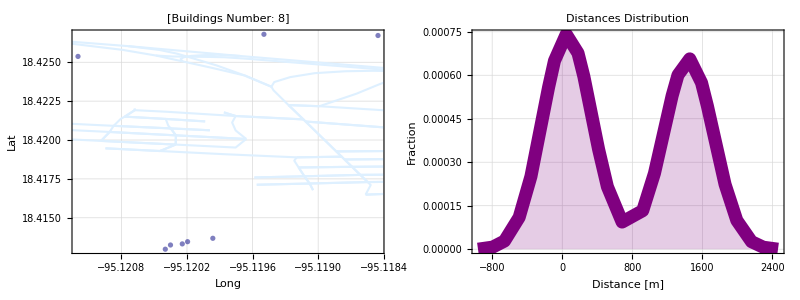

PaperScenarios/Realistic/Catemaco_original.csv

```mathematica
raw=Import[buildingPath,"Data"][[1,2,2]];
dataOriginal=Reverse[Mean/@(#//Transpose)]&/@raw[[All,1,1]];
buildingsPlot=Show[
ListPlot[dataOriginal,
AspectRatio->1,
GridLines->Automatic,
BaseStyle->Directive["Gray",25],
Frame->True,
FrameTicksStyle->15,
FrameStyle->Thick,
FrameLabel->{"Long","Lat"},
PlotStyle->{Darker[Blue,.5],PointSize[.005],Opacity[.5]},
ImageSize->750,
PlotLabel->Style[("[Buildings Number: "<>ToString [dataOriginal//Length]<>"]"),25]
],
roadsGraphic
];
geoDistances=ParallelTable[
UnitConvert[GeoDistance[Reverse[dataOriginal[[i]]],Reverse[#],UnitSystem->"Metric"],"Meters"][[1]]&/@dataOriginal
,{i,1,dataOriginal//Length}];
distancesDistribution=SmoothHistogram[Flatten[geoDistances],
GridLines->Automatic,
Frame->True,
BaseStyle->Directive["Gray",25],
AspectRatio->1,
FrameStyle->Thick,
PerformanceGoal->"Speed",
FrameTicksStyle->15,
PlotStyle->Directive[Purple,Thickness[.0125]],
PlotLabel->"Distances Distribution",
ImageSize->750,
Filling->Bottom,
FrameLabel->{"Distance [m]","Fraction"}
];
originalGrid=Grid[{{buildingsPlot,distancesDistribution}}]
Export["PaperScenarios/Realistic/"<>placeName<>"_original.csv",dataOriginal]
```

## Load and Run Buildings Data

### 01) Filter

```mathematica
sampleSize=filteringPoints;
sampled=RandomSample[dataOriginal,sampleSize];
filteredBuildings=ListPlot[
{dataOriginal,sampled(*Table[Callout[sampled[[i]],i,LeaderSize->50,CalloutStyle->Thin,Background->None],{i,1,Length[sampled]}]*)},
GridLines->Automatic,
Frame->True,
AspectRatio->1,
FrameStyle->Thick,
FrameTicksStyle->15,
BaseStyle->Directive["Gray",25],
FrameLabel->{"Long","Lat"},
PlotStyle->{Directive[{Red,PointSize[.0075],Opacity[.1]}],Directive[{Blue,PointSize[.0075],Opacity[.5]}]},
ImageSize->750,
PlotLabel->Style[("[Original Buildings Number: "<>ToString [dataOriginal//Length]<>"] :: [Filtered Number: "<>ToString[sampleSize]<>"]"),25]
];
geoDistancesFiltered=ParallelTable[
UnitConvert[GeoDistance[Reverse[sampled[[i]]],Reverse[#],UnitSystem->"Metric"],"Meters"][[1]]&/@sampled
,{i,1,sampled//Length}];
distancesDistributionFiltered=SmoothHistogram[Flatten[geoDistancesFiltered],
GridLines->Automatic,
Frame->True,
BaseStyle->Directive["Gray",25],
AspectRatio->1,
FrameStyle->Thick,
PerformanceGoal->"Speed",
FrameTicksStyle->15,
PlotStyle->Directive[Purple,Thickness[.0125]],
PlotLabel->"Distances Distribution",
ImageSize->750,
Filling->Bottom,
FrameLabel->{"Distance [m]","Fraction"}
];
filteredGrid=Grid[{{Show[filteredBuildings,roadsGraphic],distancesDistributionFiltered}}];
Export["PaperScenarios/Realistic/"<>placeName<>"_filtered.csv",sampled]
```

RandomSample::smplen: RandomSample cannot generate a sample of length 500, which is greater than the length of the sample set {{-95.1185,18.4267},{-95.1195,18.4268},{-95.1212,18.4254},{-95.12,18.4137},{-95.1202,18.4135},{-95.1202,18.4133},{-95.1204,18.4133},{-95.1204,18.413}}. If you want a choice of possibly repeated elements from the set, use RandomChoice.

ListPlot::lpn: {{{-95.1185,18.4267},{-95.1195,18.4268},{-95.1212,18.4254},{-95.12,18.4137},{-95.1202,18.4135},{-95.1202,18.4133},{-95.1204,18.4133},{-95.1204,18.413}},{}} is not a list of numbers or pairs of numbers.

RandomSample::smplen: RandomSample cannot generate a sample of length 500, which is greater than the length of the sample set {{-95.1185,18.4267},{-95.1195,18.4268},{-95.1212,18.4254},{-95.12,18.4137},{-95.1202,18.4135},{-95.1202,18.4133},{-95.1204,18.4133},{-95.1204,18.413}}. If you want a choice of possibly repeated elements from the set, use RandomChoice.

General::stop: Further output of RandomSample::smplen will be suppressed during this calculation.

ListPlot::lpn: {{{-95.1185,18.4267},{-95.1195,18.4268},{-95.1212,18.4254},{-95.12,18.4137},{-95.1202,18.4135},{-95.1202,18.4133},{-95.1204,18.4133},{-95.1204,18.413}},{}} is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

RandomSample::smplen: RandomSample cannot generate a sample of length 500, which is greater than the length of the sample set {{-95.1185,18.4267},{-95.1195,18.4268},{-95.1212,18.4254},{-95.12,18.4137},{-95.1202,18.4135},{-95.1202,18.4133},{-95.1204,18.4133},{-95.1204,18.413}}. If you want a choice of possibly repeated elements from the set, use RandomChoice.

GeoDistance::ltrng: Invalid latitude specification -95.1204.

Reverse::normal: Nonatomic expression expected at position 1 in Reverse[500].

GeoDistance::ltrng: Invalid latitude specification -95.1204.

Reverse::normal: Nonatomic expression expected at position 1 in Reverse[500].

RandomSample::lrwl: The set of items to sample from, GeoDistance[{{-95.1204,18.413},{-95.1204,18.4133},{-95.1202,18.4133},{-95.1202,18.4135},{-95.12,18.4137},{-95.1212,18.4254},{-95.1195,18.4268},{-95.1185,18.4267}},{{-95.1204,18.413},{-95.1204,18.4133},{-95.1202,18.4133},{-95.1202,18.4135},{-95.12,18.4137},{-95.1212,18.4254},{-95.1195,18.4268},{-95.1185,18.4267}},UnitSystem→Metric], should be a non-empty list or a rule weights -> choices.

Reverse::normal: Nonatomic expression expected at position 1 in Reverse[500].

General::stop: Further output of Reverse::normal will be suppressed during this calculation.

GeoDistance::invloc: Reverse[500] is not a valid location specification.

RandomSample::lrwl: The set of items to sample from, GeoDistance[Reverse[500],{{-95.1204,18.413},{-95.1204,18.4133},{-95.1202,18.4133},{-95.1202,18.4135},{-95.12,18.4137},{-95.1212,18.4254},{-95.1195,18.4268},{-95.1185,18.4267}},UnitSystem→Metric], should be a non-empty list or a rule weights -> choices.

GeoDistance::ltrng: Invalid latitude specification -95.1204.

Reverse::normal: Nonatomic expression expected at position 1 in Reverse[500].

GeoDistance::ltrng: Invalid latitude specification -95.1204.

RandomSample::lrwl: The set of items to sample from, GeoDistance[{{-95.1204,18.413},{-95.1204,18.4133},{-95.1202,18.4133},{-95.1202,18.4135},{-95.12,18.4137},{-95.1212,18.4254},{-95.1195,18.4268},{-95.1185,18.4267}},{{-95.1204,18.413},{-95.1204,18.4133},{-95.1202,18.4133},{-95.1202,18.4135},{-95.12,18.4137},{-95.1212,18.4254},{-95.1195,18.4268},{-95.1185,18.4267}},UnitSystem→Metric], should be a non-empty list or a rule weights -> choices.

Reverse::normal: Nonatomic expression expected at position 1 in Reverse[500].

GeoDistance::ltrng: Invalid latitude specification -95.1204.

General::stop: Further output of GeoDistance::ltrng will be suppressed during this calculation.

Reverse::normal: Nonatomic expression expected at position 1 in Reverse[500].

General::stop: Further output of Reverse::normal will be suppressed during this calculation.

GeoDistance::invloc: Reverse[500] is not a valid location specification.

RandomSample::lrwl: The set of items to sample from, GeoDistance[Reverse[500],{{-95.1204,18.413},{-95.1204,18.4133},{-95.1202,18.4133},{-95.1202,18.4135},{-95.12,18.4137},{-95.1212,18.4254},{-95.1195,18.4268},{-95.1185,18.4267}},UnitSystem→Metric], should be a non-empty list or a rule weights -> choices.

SmoothHistogram::ldata: {RandomSample[GeoDistance[{{-95.1204,18.413},{-95.1204,18.4133},{-95.1202,18.4133},{-95.1202,18.4135},{-95.12,18.4137},{-95.1212,18.4254},{-95.1195,18.4268},{-95.1185,18.4267}},{{-95.1204,18.413},{-95.1204,18.4133},{-95.1202,18.4133},{-95.1202,18.4135},{-95.12,18.4137},{-95.1212,18.4254},{-95.1195,18.4268},{-95.1185,18.4267}},UnitSystem→Metric],GeoDistance[{{-95.1204,18.413},{-95.1204,18.4133},{-95.1202,18.4133},{-95.1202,18.4135},{-95.12,18.4137},{-95.1212,18.4254},{-95.1195,18.4268},{-95.1185,18.4267}},Reverse[500],UnitSystem→Metric]],RandomSample[GeoDistance[Reverse[500],{{-95.1204,18.413},{-95.1204,18.4133},«5»,{-95.1185,18.4267}},UnitSystem→Metric],GeoDistance[«1»]]} is not a valid dataset or list of datasets.

General::stop: Further output of SmoothHistogram::ldata will be suppressed during this calculation.

LatitudeLongitude::invloc: GeoPosition[{{«2»},{«2»}}] is not a valid location specification.

General::stop: Further output of LatitudeLongitude::invloc will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in ….

PaperScenarios/Realistic/Catemaco_filtered.csv

### 02) Auto - Cluster

```mathematica
clusters=FindClusters[dataOriginal,Method->"NeighborhoodContraction"];
centroids=Mean/@(#//Transpose)&/@clusters;
clusterSizes=Length/@clusters;
centroids=Median/@(#//Transpose)&/@clusters;
centroidsStyles=Directive[Black,Opacity[.5],PointSize[Rescale[#//N,{Min[clusterSizes],Max[clusterSizes]},{.005,.02}]]]&/@clusterSizes;
automaticCluster=Show[{
ListPlot[clusters,
GridLines->Automatic,
Frame->True,
AspectRatio->1,
FrameStyle->Thick,
FrameTicksStyle->15,
PerformanceGoal->"Speed",
BaseStyle->Directive["Gray",25],
FrameLabel->{"Long","Lat"},
PlotStyle->Directive[{PointSize[.0075],Opacity[.5]}],
ImageSize->750,
PlotLabel->Style[("[Buildings Number: "<>ToString [dataOriginal//Length]<>"] :: [Clusters Number: "<>ToString[clusters//Length]<>"]"),25]
],
ListPlot[{#}&/@centroids,PlotStyle->centroidsStyles],
roadsGraphic
}//Flatten];
geoDistances=ParallelTable[
UnitConvert[GeoDistance[Reverse[centroids[[i]]],Reverse[#],UnitSystem->"Metric"],"Meters"][[1]]&/@centroids
,{i,1,centroids//Length}];
distancesDistributionClusteredAuto=SmoothHistogram[Flatten[geoDistances],
GridLines->Automatic,
Frame->True,
BaseStyle->Directive["Gray",25],
AspectRatio->1,
FrameStyle->Thick,
BaseStyle->Directive["Gray",25],
FrameLabel->{"Long","Lat"},
PerformanceGoal->"Speed",
FrameTicksStyle->15,
PlotStyle->Directive[Purple,Thickness[.0125]],
PlotLabel->"Distances Distribution",
ImageSize->750,
Filling->Bottom,
FrameLabel->{"Distance [m]","Fraction"}
];
automaticClusteringGrid=Grid[{{automaticCluster,distancesDistributionClusteredAuto}}];
Export["PaperScenarios/Realistic/"<>placeName<>"_autoCluster.csv",centroids]
```

PaperScenarios/Realistic/Catemaco_autoCluster.csv

### 03) Manual Cluster

```mathematica
{clustersNumber,method}={manualPoints,Automatic};
clusters=FindClusters[dataOriginal,clustersNumber,Method-> method];
clusterSizes=Length/@clusters;
centroids=Median/@(#//Transpose)&/@clusters;
centroidsStyles=Directive[Black,Opacity[.5],PointSize[Rescale[#//N,{Min[clusterSizes],Max[clusterSizes]},{.0025,.015}]]]&/@clusterSizes;
clusteredManual=Show[{
roadsGraphic,
ListPlot[clusters,
PlotStyle->Directive[{PointSize[.0075],Opacity[.25]}]
],
ListPlot[{#}&/@centroids,PlotStyle->centroidsStyles]
}//Flatten,
GridLines->Automatic,
Frame->True,
AspectRatio->1,
BaseStyle->Directive["Gray",25],
FrameLabel->{"Long","Lat"},
FrameStyle->Thick,
FrameTicksStyle->15,
ImageSize->750,
PlotLabel->Style[("[Buildings Number: "<>ToString [dataOriginal//Length]<>"] :: [Clusters Number: "<>ToString[clusters//Length]<>"]"),25]];
clusteredManualFinal=Show[
roadsGraphic,
clusteredManual,
ListPlot[Table[Callout[centroids[[i]],i],{i,1,Length[centroids]}],PlotStyle->centroidsStyles],
GridLines->Automatic,
Frame->True,
BaseStyle->Directive["Gray",25],
FrameLabel->{"Long","Lat"},
AspectRatio->1,
FrameStyle->Thick,
PerformanceGoal->"Speed",
FrameTicksStyle->15,
ImageSize->750,
PlotLabel->Style[("[Buildings Number: "<>ToString [dataOriginal//Length]<>"] :: [Clusters Number: "<>ToString[clusters//Length]<>"]"),25]
];
geoDistances=ParallelTable[
UnitConvert[GeoDistance[Reverse[centroids[[i]]],Reverse[#],UnitSystem->"Metric"],"Meters"][[1]]&/@centroids
,{i,1,centroids//Length}];
distancesDistributionClustered=SmoothHistogram[Flatten[geoDistances],
GridLines->Automatic,
Frame->True,
BaseStyle->Directive["Gray",25],
AspectRatio->1,
FrameStyle->Thick,
PerformanceGoal->"Speed",
FrameTicksStyle->15,
PlotStyle->Directive[Purple,Thickness[.0125]],
PlotLabel->"Distances Distribution",
ImageSize->750,
Filling->Bottom,
FrameLabel->{"Distance [m]","Fraction"}
];
manualClusteringGrid=Grid[{{clusteredManual,distancesDistributionClustered}}];
Export["PaperScenarios/Realistic/"<>placeName<>"_manualClusters.csv",clusters]
Export["PaperScenarios/Realistic/"<>placeName<>"_manualClustersCentroids.csv",centroids]
Export["PaperScenarios/Realistic/"<>placeName<>"_manualClustersSizes.csv",clusterSizes]
```

PaperScenarios/Realistic/Catemaco_manualClusters.csv

PaperScenarios/Realistic/Catemaco_manualClustersCentroids.csv

PaperScenarios/Realistic/Catemaco_manualClustersSizes.csv

### 04) Voronoi

```mathematica
clusteredMap=ListPlot[clusters,PlotStyle->Directive[{PointSize[.002],Opacity[1]}]];
VoronoiMesh[dataOriginal,PlotTheme->"Lines",MeshCellHighlight->{{1,All}->Directive[Blue,Thickness[.0015],Opacity[.2]],{0,All}->None}];
voronoi=Show[%,roadsGraphic,clusteredMap,Graphics[{Black,Opacity[1],PointSize[.0025],Point[dataOriginal]}],ImageSize->1000,AspectRatio->1];
```

## Transition Probabilities

### Matrix

```mathematica
stayForce=100;
(**)
data=sampled;
distances=geoDistancesFiltered;
distancesMatrix=distances//MatrixPlot[#,ColorFunction->"LakeColors",BaseStyle->20,ImageSize->1000]&;
(**)
thresheld=Table[If[#<1000,#,0]&/@i,{i,distances}];
thresheld//MatrixPlot[#,ColorFunction->"LakeColors",BaseStyle->20,ImageSize->1000]&;
probabilitiesRaw=Quiet[(#/Total[#])]&/@thresheld;
probabilities=((#/Total[#])&/@ReplacePart[probabilitiesRaw,{i_,i_}->stayForce]);
probabilitiesMatrix=MatrixPlot[probabilities,ColorFunction->"LakeColors",BaseStyle->20,ImageSize->1000,PlotLegends->Automatic];
Export["PaperScenarios/Realistic/"<>placeName<>"TransitionsMatrix.csv",probabilities]
```

MatrixPlot::mat0: Argument {RandomSample[GeoDistance[{{-95.1204,18.413},{-95.1204,18.4133},{-95.1202,18.4133},{-95.1202,18.4135},{-95.12,18.4137},{-95.1212,18.4254},{-95.1195,18.4268},{-95.1185,18.4267}},{{-95.1204,18.413},{-95.1204,18.4133},{-95.1202,18.4133},{-95.1202,18.4135},{-95.12,18.4137},{-95.1212,18.4254},{-95.1195,18.4268},{-95.1185,18.4267}},UnitSystem→Metric],GeoDistance[{{-95.1204,18.413},{-95.1204,18.4133},{-95.1202,18.4133},{-95.1202,18.4135},{-95.12,18.4137},{-95.1212,18.4254},{-95.1195,18.4268},{-95.1185,18.4267}},Reverse[500],UnitSystem→Metric]],RandomSample[GeoDistance[Reverse[500],{{-95.1204,18.413},{-95.1204,18.4133},«5»,{-95.1185,18.4267}},UnitSystem→Metric],GeoDistance[«1»]]} at position 1 is not a matrix.

RandomSample::lrwl: The set of items to sample from, If[GeoDistance[{{-95.1204,18.413},{-95.1204,18.4133},{-95.1202,18.4133},{-95.1202,18.4135},{-95.12,18.4137},{-95.1212,18.4254},{-95.1195,18.4268},{-95.1185,18.4267}},{{-95.1204,18.413},{-95.1204,18.4133},{-95.1202,18.4133},{-95.1202,18.4135},{-95.12,18.4137},{-95.1212,18.4254},{-95.1195,18.4268},{-95.1185,18.4267}},UnitSystem→Metric]<1000,GeoDistance[{{-95.1204,18.413},{-95.1204,18.4133},{-95.1202,18.4133},{-95.1202,18.4135},{-95.12,18.4137},{-95.1212,18.4254},{-95.1195,18.4268},{-95.1185,18.4267}},«1»,UnitSystem→Metric],0], should be a non-empty list or a rule weights -> choices.

RandomSample::lrwl: The set of items to sample from, If[GeoDistance[Reverse[500],{{-95.1204,18.413},{-95.1204,18.4133},{-95.1202,18.4133},{-95.1202,18.4135},{-95.12,18.4137},{-95.1212,18.4254},{-95.1195,18.4268},{-95.1185,18.4267}},UnitSystem→Metric]<1000,GeoDistance[Reverse[500],{{-95.1204,18.413},{-95.1204,18.4133},{-95.1202,18.4133},{-95.1202,18.4135},{-95.12,18.4137},{-95.1212,18.4254},{-95.1195,18.4268},{-95.1185,18.4267}},UnitSystem→Metric],0], should be a non-empty list or a rule weights -> choices.

MatrixPlot::mat0: Argument {RandomSample[If[GeoDistance[{{-95.1204,18.413},{-95.1204,18.4133},{-95.1202,18.4133},{-95.1202,18.4135},{-95.12,18.4137},{-95.1212,18.4254},{-95.1195,18.4268},{-95.1185,18.4267}},{{-95.1204,18.413},{-95.1204,18.4133},{-95.1202,18.4133},{-95.1202,18.4135},{-95.12,18.4137},{-95.1212,18.4254},{-95.1195,18.4268},{-95.1185,18.4267}},UnitSystem→Metric]<1000,GeoDistance[{{-95.1204,18.413},{-95.1204,18.4133},{-95.1202,18.4133},{-95.1202,18.4135},{-95.12,18.4137},{-95.1212,18.4254},{-95.1195,18.4268},{-95.1185,18.4267}},{{-95.1204,18.413},{-95.1204,18.4133},{-95.1202,18.4133},«3»,{-95.1195,18.4268},{-95.1185,18.4267}},UnitSystem→Metric],0],If[«1»]],«1»} at position 1 is not a matrix.

MatrixPlot::mat0: Argument {(100 «1»)/(100+RandomSample[If[GeoDistance[{«8»},{«8»},Rule[«2»]]<1000,GeoDistance[{{«2»},{«2»},{«2»},{«2»},{«2»},{«2»},{«2»},{«2»}},{{«2»},{«2»},{«2»},{«2»},{«2»},{«2»},{«2»},{«2»}},UnitSystem→Metric],0],If[GeoDistance[{«8»},Reverse[«1»],Rule[«2»]]<1000,GeoDistance[{{«2»},{«2»},{«2»},{«2»},{«2»},{«2»},{«2»},{«2»}},Reverse[500],UnitSystem→Metric],0]]),100/((«1») (100+1/(If[GeoDistance[«3»]<1000,GeoDistance[Reverse[«1»],{«8»},Rule[«2»]],0]+If[GeoDistance[«3»]<1000,GeoDistance[Reverse[«1»],Reverse[«1»],Rule[«2»]],0])))} at position 1 is not a matrix.

PaperScenarios/Realistic/CatemacoTransitionsMatrix.csv

### Network

```mathematica
(*probabilitiesNetwork=GraphTransitionsFrequenciesWithMax[
{
probabilities,
ToString/@Range[probabilities//Length]
},Max[Max/@probabilities]/6.5,
VariableStyle->"Both",
VertexCoordinates->centroids,
ImageSize->1000,
LineThickness->.0005,
VertexLabelStyle->.001,
VertexStyle->Directive[{EdgeForm[Directive[{Thickness[.001],White}]],Opacity[1],Darker[White,1]}],
VertexSize->.01,
Background->White(*Lighter[LightBlue,.9]*),
ImagePadding->0,
Prolog->{Thickness[.0015],Gray,Opacity[.25],rawRoad}
];
clusteredManual2=Show[{
ListPlot[clusters,
GridLines->Automatic,
Frame->True,
AspectRatio->1,
FrameStyle->Thick,
FrameTicksStyle->15,
PlotStyle->Directive[{PointSize[.0075],Opacity[.2]}],
ImageSize->1000,
PlotLabel->Style[("[Buildings Number: "<>ToString [dataOriginal//Length]<>"] :: [Clusters Number: "<>ToString[clusters//Length]<>"]"),25]
],
ListPlot[{#}&/@centroids,PlotStyle->centroidsStyles,AspectRatio->1]
}//Flatten];
probabilitiesNetworkFinal=Show[probabilitiesNetwork,clusteredManual2,
GridLines->Automatic,
Frame->True,
FrameStyle->Thick,
AspectRatio->1,
PerformanceGoal->"Speed",
FrameTicksStyle->15,
PlotStyle->Directive[{PointSize[.0075],Opacity[.1]}],
ImageSize->1000,
PlotLabel->Style[("[Buildings Number: "<>ToString [dataOriginal//Length]<>"] :: [Clusters Number: "<>ToString[clusters//Length]<>"]"),25]
]*)
```

## Export Maps

```mathematica
Export["PaperScenarios/Realistic/images/"<>placeName<>"_00_original.png",originalGrid,ImageSize->imageSize,ImageResolution->imageResolution]
Export["PaperScenarios/Realistic/images/"<>placeName<>"_01_clusteredAuto.png",automaticClusteringGrid,ImageSize->imageSize,ImageResolution->imageResolution]
Export["PaperScenarios/Realistic/images/"<>placeName<>"_02_clusteredManual.png",manualClusteringGrid,ImageSize->imageSize,ImageResolution->imageResolution]
Export["PaperScenarios/Realistic/images/"<>placeName<>"_03_filtered.png",filteredGrid,ImageSize->imageSize,ImageResolution->imageResolution]
Export["PaperScenarios/Realistic/images/"<>placeName<>"_04_voronoi.png",voronoi,ImageSize->imageSize,ImageResolution->imageResolution]
(*Export["ProbabilitiesMatrices/images/"<>placeName<>"_02_clusteredManual.png",clusteredManual,ImageSize->imageSize,ImageResolution->imageResolution]*)
(*Export["ProbabilitiesMatrices/images/"<>placeName<>"_02Buildings_original_ClusteredManualFinal.png",manualClusteringGrid,ImageSize->imageSize,ImageResolution->imageResolution]*)
(*Export["ProbabilitiesMatrices/images/"<>placeName<>"_02Buildings_original_ClusteredManualTagged.png",clusteredManualFinal,ImageSize->imageSize,ImageResolution->imageResolution]*)
(*Export["ProbabilitiesMatrices/images/"<>placeName<>"_06_probabilitiesNetwork.png",probabilitiesNetworkFinal,ImageSize->imageSize,ImageResolution->imageResolution]*)
(*Export["ProbabilitiesMatrices/images/"<>placeName<>"_07_DistancesDistribution.png",distancesDistribution,ImageSize->imageSize,ImageResolution->imageResolution]*)
(*Export["ProbabilitiesMatrices/images/"<>placeName<>"_04Buildings_original_TaggedClusters.png",taggedClusters,ImageSize->imageSize,ImageResolution->imageResolution]*)
Export["PaperScenarios/Realistic/images/"<>placeName<>"_07_matrixDistances.png",distancesMatrix,ImageSize->imageSize,ImageResolution->imageResolution]
Export["PaperScenarios/Realistic/images/"<>placeName<>"_07_matrixProbabilities.png",probabilitiesMatrix,ImageSize->imageSize,ImageResolution->imageResolution]
```

PaperScenarios/Realistic/images/Catemaco_00_original.png

PaperScenarios/Realistic/images/Catemaco_01_clusteredAuto.png

PaperScenarios/Realistic/images/Catemaco_02_clusteredManual.png

PaperScenarios/Realistic/images/Catemaco_03_filtered.png

PaperScenarios/Realistic/images/Catemaco_04_voronoi.png

PaperScenarios/Realistic/images/Catemaco_07_matrixDistances.png

PaperScenarios/Realistic/images/Catemaco_07_matrixProbabilities.png